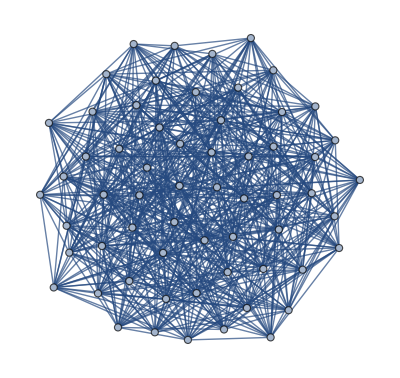

```mathematica
G=Import["/home/josera/owncloud2/clientsync/InvesEnCurso/eta/K4J9.g6"]
```

```mathematica
v=VertexCount[G]
```

61

```mathematica
VertexTransitiveGraphQ[G]
```

True

```mathematica
VertexDegree[G]
```

{20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20}

```mathematica
alpha=Length@FindIndependentVertexSet[G][[1]]
```

8

```mathematica
omega=Length@FindIndependentVertexSet[GraphComplement[G]][[1]]
```

3

```mathematica
eta=2*alpha/(alpha+(v/omega))
```

48/85

```mathematica
N[%]
```

0.564706